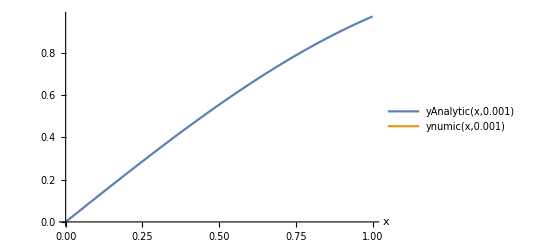

```mathematica
ϵ=0.001;
ynumic[x_,ϵ_] = NDSolve[{y''[x]+(1+ϵ)y[x]==ϵ y[x]^3 , y[0]==0, y'[0]==2/3^(1/2)},y,{x,0,1}];
Clear[x]
Clear[ϵ]
yAnalytic[x_, ϵ_] = (2/3^(1/2))* Sin[x] +(ϵ (2/3)*Sin[3x]);
Plot[{yAnalytic[x,0.001],ynumic[x,0.001]} ,{x,0,1}, PlotLegends ->"Expressions", AxesLabel-> Automatic]
```

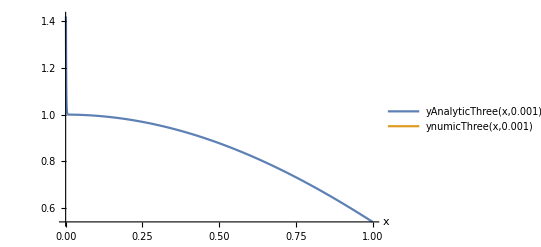

```mathematica
ϵ=0.001;
ynumicThree[x_,ϵ_] = NDSolve[{ϵ y'[x]+y[x]==Cos[x] , y[0]==2},y,{x,0,1}];
Clear[x]
Clear[ϵ]
yAnalyticThree[x_, ϵ_] =  Cos[x]+Exp[-x/ϵ];
Plot[{yAnalyticThree[x,0.001],ynumicThree[x,0.001]} ,{x,0,1}, PlotLegends ->"Expressions", AxesLabel-> Automatic]
```

NDSolve::bvluc: The equations derived from the boundary conditions are numerically ill-conditioned. The boundary conditions may not be sufficient to uniquely define a solution. If a solution is computed, it may match the boundary conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 9063.21 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

-1+3 ⅇ^((-1+x)/(√ϵ))+ⅇ^(-x/(√ϵ))

General::munfl: Exp[-999.98] is too small to represent as a normalized machine number; precision may be lost.

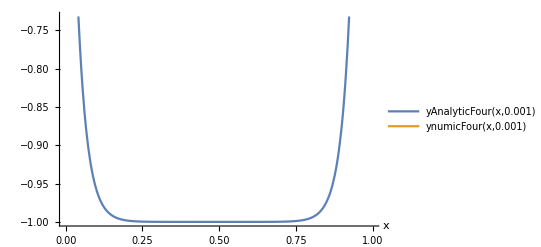

```mathematica
ϵ=0.001;
ynumicFour[x_,ϵ_] = NDSolve[{ϵ y''[x]-y[x]==-1 , y[0]==0, y[1]==2},y,{x,0,1}];
Clear[x]
Clear[ϵ]
yAnalyticFour[x_, ϵ_] =  Exp[-x/(ϵ^(1/2))]+3 * Exp[(x-1)/(ϵ^(1/2))] -1
Plot[{yAnalyticFour[x,0.001],ynumicFour[x,0.001]} ,{x,0,1}, PlotLegends ->"Expressions", AxesLabel-> Automatic]
```

General::munfl: Exp[-999.98] is too small to represent as a normalized machine number; precision may be lost.

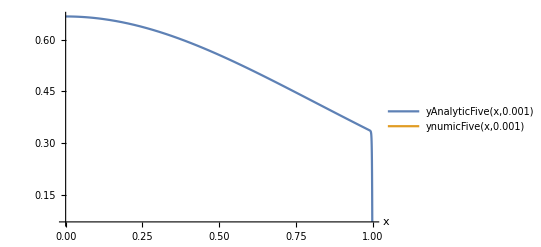

```mathematica
ϵ=0.001;
ynumicFive[x_,ϵ_] =NDSolve[{ϵ y''[x]-y'[x]-x y[x]^2==0 , y[0]==1, y[1]==0},y,{x,0,1}];
Clear[x]
Clear[ϵ]
yAnalyticFive[x_, ϵ_] =  (2/(x^2 + 2)) - (1/3) - (2/3) Exp[(x-1)/ϵ];
Plot[{yAnalyticFive[x,0.001],ynumicFive[x,0.001]} ,{x,0,1}, PlotLegends ->"Expressions", AxesLabel-> Automatic]
```

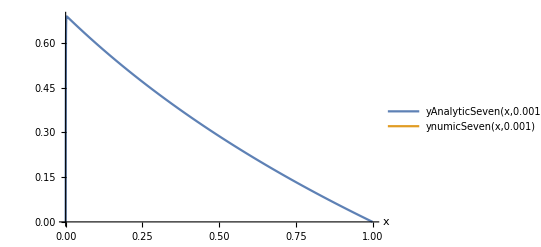

```mathematica
ϵ=0.001;
ynumicSeven[x_,ϵ_] =NDSolve[{ϵ y''[x]+2y'[x]+ Exp[y[x]]==0 , y[0]==0, y[1]==0},y,{x,0,1}];
Clear[x]
Clear[ϵ]
yAnalyticSeven[x_, ϵ_] =  -Log[x+1]+Log[2] -Log[2]*Exp[-2x/ϵ];
Plot[{yAnalyticSeven[x,0.001],ynumicSeven[x,0.001]} ,{x,0,1}, PlotLegends ->"Expressions", AxesLabel-> Automatic]
```

```mathematica
DSolve[{ y''[x]-y'[x]==0, y[0]==1},y,{x,0,1}]
```

{{y→Function[{x},1+(-1+ⅇ^x) C[1]]}}